# Pchem Assignment 5 – 7 November 2016

## Question 1

```mathematica
tdnatall = Transpose[Import[ "/Users/Research/JHU_Class_Material/pchem/assignment_5/TDenat.xlsx","Data"]];
tdnat=Transpose[tdnatall[[2;;]]][[1]];
```

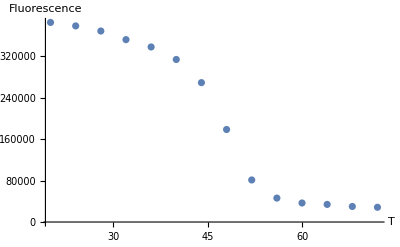

```mathematica
(*Plot the denaturation data*)
tdnatplot=ListPlot[tdnat,PlotRange->All,AxesLabel->{"T","Fluorescence"}]
```

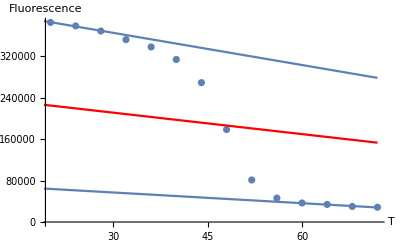

```mathematica
(*Fit the denaturation data to two baselines. Pick the first and last few points that would make linear baselines
we want the baselines so we can calculate a and b
b/a = fu/fn = Keq
b is the distance between fn and fm. proporional to U
a is the distance between fu and fm. proportional to N*) 
(*So Tm is around 48*)
(*native baseline uses the first few points*)
ln=LinearModelFit[tdnat[[1;;3]],x,x];
fn[x_]:=ln["BestFitParameters"][[1]]+(ln["BestFitParameters"][[2]]*x);
(*unfolded baseline uses the last few points*)
lu=LinearModelFit[tdnat[[-3;;]],x,x];
fu[x_]:=lu["BestFitParameters"][[1]]+(lu["BestFitParameters"][[2]]*x);
(*The midpoint line is halfway between the equations that describe the fn and fu lines*)
lm=Table[ {x,((ln[x]-lu[x])/2)+lu[x]},{x,0,Max[tdnat[[All,1]]]}];
Show[tdnatplot,Plot[ln[x],{x,0,Max[tdnat[[All,1]]]}],Plot[lu[x],{x,0,Max[tdnat[[All,1]]]}],ListLinePlot[lm,PlotStyle->Red]]
```

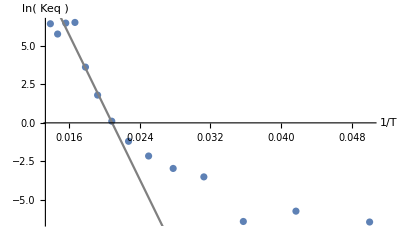

inverse of x-intercept = Tm = 47.9064

```mathematica
(*The x-intercept is the Tm. dG = 0 at Keq = 1 at Tm
dG = -RTln(Keq)
ln(Keq) = ( -dG/R )(1/T)
y = mx + b
	but this doesn't actually make sense so never mind...
*)
(*b is the fraction native fit minus the y data*)
b=fn[tdnat[[All,1]]]-tdnat[[All,2]];
(*a is the y data minus the fraction unfolded fit*)
a=tdnat[[All,2]]-fu[tdnat[[All,1]]];
(*x1 y1 where x is 1/T and y is ln(b/a) (which is fu/fn = Keq)*)
lnkvsinvtdata=Transpose[{(1/tdnat[[All,1]]),Re[Log[b/a]]}];
lnkvsinvt=ListPlot[lnkvsinvtdata];
(*get the best fit line of where the data is linear. This is where unfolding is happening and you're getting b/a*)
lm2=LinearModelFit[lnkvsinvtdata[[-7;;-5]],x,x];
Show[lnkvsinvt,Plot[lm2[x],{x,Min[lnkvsinvtdata],Max[lnkvsinvtdata]},PlotStyle->Gray],AxesLabel->{"1/T","ln( Keq )"}]
(*y=mx+b --> ((y-b)/m)=x --> 1/((y-b)/m)=Tm*)
Print["inverse of x-intercept = Tm = ",tm =1/(( 0-lm2["BestFitParameters"][[1]])/lm2["BestFitParameters"][[2]])]
```

## Question 2

```mathematica
(*part b of this question needs the b/a thing that gets Keq and then you get dG from that. Do dG vs x where the y-int is dgh20. Get dG by doing the dG = -RTln(k) equation*)
chemdenat1 = Transpose[Transpose[Import[ "/Users/Research/JHU_Class_Material/pchem/assignment_5/chemdenatdata1","Data"]][[3;;]]][[1]];
```

```mathematica
(*store the raw data plot*)
chemdenat1plot = ListPlot[chemdenat1,PlotRange->All,AxesLabel->{"[GdnHCl]","fluorescence"}];
```

```mathematica
(*values and functions needed to get best fit curve*)
R=0.0019872041;
T=288.15;
dg=dgh2o+m*denat;
k=Exp[-dg/(R*T)];
fn=k/(1+k);
fd=1/(1+k);
yn=an+bn*denat;
yd=ad+bd*denat;
yobs=fn*yn+fd*yd;
```

```mathematica
(*get the best fit line using some guesses from the raw data graph and copying what Doug did in class*)
nlmchemdenat1=NonlinearModelFit[chemdenat1,yobs,
{
{an,8},
{bn,-0.25},
{ad,1},
{bd,-0.02},
{dgh2o,0},
{m,0}
},
denat];
```

```mathematica
(*check the parameters*)
nlmchemdenat1["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
an | 7.9214 | 0.00590286 | 1341.96 | 1.40399×10^-92
bn | -0.13738 | 0.00496016 | -27.6966 | 2.91735×10^-27
ad | 1.08241 | 0.0277132 | 39.0577 | 6.98662×10^-33
bd | -0.0418501 | 0.00770027 | -5.43488 | 3.15101×10^-6
dgh2o | -12.1427 | 0.0599425 | -202.572 | 1.46199×10^-60
m | 4.9885 | 0.0247218 | 201.786 | 1.70121×10^-60

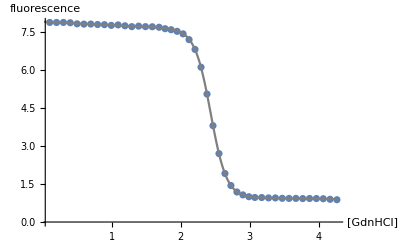

```mathematica
(*graph the best fit line over the raw data*)
Show[chemdenat1plot,Plot[nlmchemdenat1[denat],{denat,0,Max[chemdenat1[[All,1]]]},PlotStyle->Gray]]
```

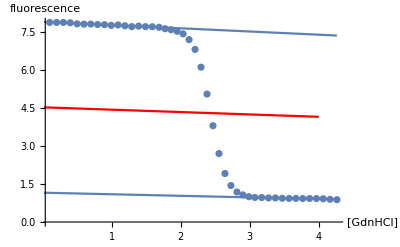

```mathematica
(*native baseline uses the first few points*)
lnchemdenat1=LinearModelFit[chemdenat1[[1;;17]],x,x];
fnchemdenat1[x_]:=lnchemdenat1["BestFitParameters"][[1]]+(lnchemdenat1["BestFitParameters"][[2]]*x);
(*unfolded baseline uses the last few points*)
luchemdenat1=LinearModelFit[chemdenat1[[-13;;]],x,x];
fuchemdenat1[x_]:=luchemdenat1["BestFitParameters"][[1]]+(luchemdenat1["BestFitParameters"][[2]]*x);
(*The midpoint line is halfway between the equations that describe the fn and fu lines*)
lmchemdenat1=Table[ {x,((lnchemdenat1[x]-luchemdenat1[x])/2)+luchemdenat1[x]},{x,0,Max[chemdenat1[[All,1]]]}];
Show[chemdenat1plot,Plot[lnchemdenat1[x],{x,0,Max[chemdenat1[[All,1]]]}],Plot[luchemdenat1[x],{x,0,Max[chemdenat1[[All,1]]]}],
ListLinePlot[lmchemdenat1,PlotStyle->Red]]
```

```mathematica
(*b is the fraction native fit minus the y data*)
bchemdenat1=fnchemdenat1[chemdenat1[[All,1]]]-chemdenat1[[All,2]];
(*a is the y data minus the fraction unfolded fit*)
achemdenat1=chemdenat1[[All,2]]-fuchemdenat1[chemdenat1[[All,1]]];
(*get x1 y1 where x is [GdnHCl] and y is -RTln(b/a) (b/a = fu/fn = Keq)*)
dgvschemdenat1=Transpose[{chemdenat1[[All,1]],-R*T*Re[Log[bchemdenat1/achemdenat1]]}];
(*we know dGh2o is around -12*)
dgvschemdenat1p=ListPlot[dgvschemdenat1,AxesLabel->{"[GdnHCl]","dG"},PlotRange->{{0,5},{-12,12}}];
```

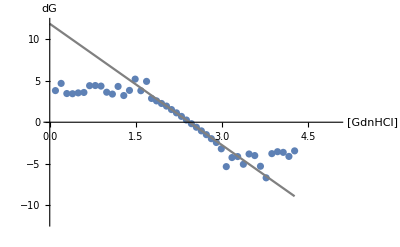

dG is about 11.8424

```mathematica
(*get the best fit line of the dG vs [GdnHCl] plot where it is most linear (where it is unfolding and you're getting the actual b/a values)*)
dgvschemdenat1fit=LinearModelFit[dgvschemdenat1[[21;;26]],x,x];
Show[dgvschemdenat1p,Plot[dgvschemdenat1fit[denat],{denat,0,Max[chemdenat1[[All,1]]]},PlotStyle->Gray,PlotRange->{{0,5},{-12,12}}]]
Print["dG is about ", dgvschemdenat1fit[0]]
```

## Question 5

```mathematica
(*normalized the chemdenat1 data from Q2*)
min=Min[chemdenat1[[All,2]]];
max=Max[chemdenat1[[All,2]]];
fluornorm=Table[ (y-min)/(max-min),{y,chemdenat1[[All,2]]}];
chemdenat1norm=Transpose[{chemdenat1[[All,1]],fluornorm}];
chemdenat1normp=ListPlot[chemdenat1norm,AxesLabel->{"[GdnHCl]","Fluorescence normed"}];
```

```mathematica
(*fit the data again*)
(*get the best fit line using some guesses from the raw data graph and copying what Doug did in class*)
nlmchemdenat1normfit=NonlinearModelFit[chemdenat1norm,yobs,
{
{an,1},
{bn,-0.25},
{ad,0.1},
{bd,-0.02},
{dgh2o,0},
{m,0}
},
denat];
nlmchemdenat1normfit["ParameterTable"]
Print["dGh2o and m did not change with normalizing the data"]
```

| Estimate | Standard Error | t-Statistic | P-Value
an | 0.0287102 | 0.00395245 | 7.2639 | 9.33021×10^-9
bn | -0.00596866 | 0.00109821 | -5.43488 | 3.15101×10^-6
ad | 1.00409 | 0.000841865 | 1192.69 | 1.39492×10^-90
bd | -0.0195931 | 0.000707418 | -27.6966 | 2.91735×10^-27
dgh2o | 12.1427 | 0.0599425 | 202.572 | 1.46199×10^-60
m | -4.9885 | 0.0247218 | -201.786 | 1.70121×10^-60

dGh2o and m did not change with normalizing the data

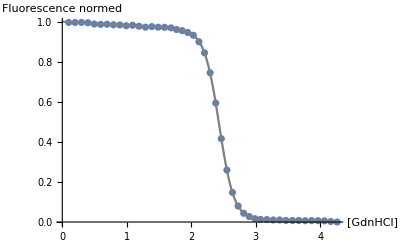

```mathematica
(*plot the fit data along the normalized data*)
Show[chemdenat1normp,Plot[nlmchemdenat1normfit[denat],{denat,0,Max[chemdenat1norm[[All,1]]]},PlotStyle->Gray]]
```

```mathematica
Question 6
```

Removing data from the N end. I thought it was supposed to have a large effect on dG, but it doesn't seem to

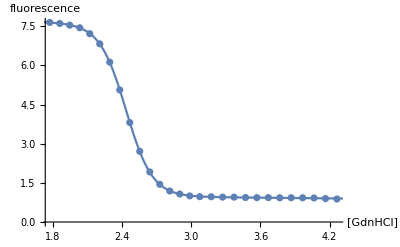

| Estimate | Standard Error | t-Statistic | P-Value
an | 7.8968 | 0.0913564 | 86.4395 | 2.35136×10^-29
bn | -0.133463 | 0.0486392 | -2.74395 | 0.0118472
ad | 1.09535 | 0.0216658 | 50.5564 | 2.95206×10^-24
bd | -0.045235 | 0.00598201 | -7.56184 | 1.48439×10^-7
dgh2o | -12.2268 | 0.0711495 | -171.847 | 6.54492×10^-36
m | 5.02191 | 0.0277267 | 181.122 | 2.0607×10^-36

```mathematica
(*
(*remove points on the native side*)
*)
chemdenat1removen = chemdenat1[[18;;]];
(*native baseline uses the first few points*)
lnchemdenat1rn=LinearModelFit[chemdenat1removen[[1;;5]],x,x];
fnchemdenat1rn[x_]:=lnchemdenat1rn["BestFitParameters"][[1]]+(lnchemdenat1rn["BestFitParameters"][[2]]*x);
(*The midpoint line is halfway between the equations that describe the fn and fu lines*)
lmchemdenat1nend=Table[ {x,((lnchemdenat1rn[x]-luchemdenat1[x])/2)+luchemdenat1[x]},{x,0,Max[chemdenat1removen[[All,1]]]}];
Print["Removing data from the N end. I thought it was supposed to have a large effect on dG, but it doesn't seem to"]
Show[ListPlot[chemdenat1removen],Plot[lnchemdenat1rn[x],{x,0,Max[chemdenat1removen[[All,1]]]},PlotStyle->Gray],Plot[luchemdenat1[x],{x,0,Max[chemdenat1removen[[All,1]]]}],
ListLinePlot[lmchemdenat1nend,PlotStyle->Red],AxesLabel->{"[GdnHCl]","Fluorescence"}];
(*get the best fit line using some guesses from the raw data graph and copying what Doug did in class*)
nlmchemdenat1nend=NonlinearModelFit[chemdenat1removen,yobs,
{
{an,8},
{bn,-0.25},
{ad,1},
{bd,-0.02},
{dgh2o,0},
{m,0}
},
denat];
(*show the fit*)
Show[ListPlot[chemdenat1removen,AxesLabel->{"[GdnHCl]","fluorescence"}],Plot[nlmchemdenat1nend[x],{x,0,5}]]
nlmchemdenat1nend["ParameterTable"]
```

Removing data from the U end. I thought it was supposed to have a large effect on dG, but it doesn't seem to

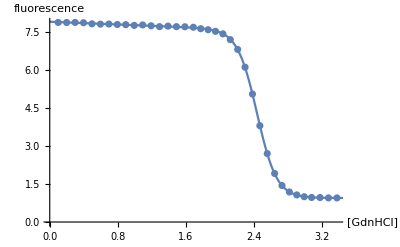

| Estimate | Standard Error | t-Statistic | P-Value
an | 7.92035 | 0.00608208 | 1302.24 | 7.51123×10^-73
bn | -0.135894 | 0.00517608 | -26.2541 | 2.96334×10^-22
ad | 0.963787 | 0.0955203 | 10.0899 | 3.71315×10^-11
bd | -0.00418396 | 0.0304828 | -0.137257 | 0.891745
dgh2o | -12.0849 | 0.0718168 | -168.274 | 3.38373×10^-46
m | 4.96262 | 0.030426 | 163.105 | 8.61926×10^-46

```mathematica
(*
(*repeating the same exact thing but from the U side...*)
*)
chemdenat1removeu = chemdenat1[[;;-10]];
(*native baseline uses the first few points*)
luchemdenat1ru=LinearModelFit[chemdenat1removeu[[-5;;]],x,x];
fuchemdenat1ru[x_]:=luchemdenat1ru["BestFitParameters"][[1]]+(luchemdenat1ru["BestFitParameters"][[2]]*x);
(*The midpoint line is halfway between the equations that describe the fn and fu lines*)
lmchemdenat1uend=Table[ {x,((lnchemdenat1[x]-luchemdenat1ru[x])/2)+luchemdenat1ru[x]},{x,0,Max[chemdenat1removeu[[All,1]]]}];
Print["Removing data from the U end. I thought it was supposed to have a large effect on dG, but it doesn't seem to"]
Show[ListPlot[chemdenat1removeu],Plot[lnchemdenat1[x],{x,0,Max[chemdenat1removeu[[All,1]]]}],Plot[luchemdenat1ru[x],{x,0,Max[chemdenat1removeu[[All,1]]]},PlotStyle->Gray],
ListLinePlot[lmchemdenat1uend,PlotStyle->Red],AxesLabel->{"[GdnHCl]","Fluorescence"}];
(*get the best fit line using some guesses from the raw data graph and copying what Doug did in class*)
nlmchemdenat1uend=NonlinearModelFit[chemdenat1removeu,yobs,
{
{an,8},
{bn,-0.25},
{ad,1},
{bd,-0.02},
{dgh2o,0},
{m,0}
},
denat];
(*plot the fit*)
Show[ListPlot[chemdenat1removeu,AxesLabel->{"[GdnHCl]","fluorescence"}],Plot[nlmchemdenat1uend[x],{x,0,5}]]
nlmchemdenat1uend["ParameterTable"]
```

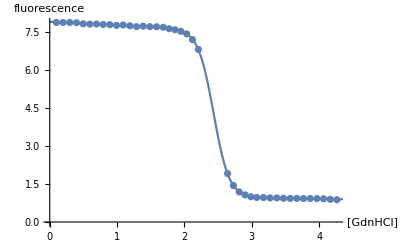

| Estimate | Standard Error | t-Statistic | P-Value
an | 7.92076 | 0.00617385 | 1282.95 | 2.29331×10^-83
bn | -0.136425 | 0.0053781 | -25.3668 | 4.04598×10^-24
ad | 1.07714 | 0.0305373 | 35.2729 | 6.05902×10^-29
bd | -0.0404775 | 0.008419 | -4.80787 | 0.0000286252
dgh2o | -12.0978 | 0.079042 | -153.055 | 4.64814×10^-51
m | 4.97077 | 0.0322851 | 153.965 | 3.77885×10^-51

```mathematica
(*
(*and again, we do this exact same thing but now in the middle*)
*)
(*native baseline uses the first few points*)
chemdenat1removemid=Drop[chemdenat1,{24,27}];
lnchemdenat1rmid=LinearModelFit[chemdenat1removemid[[1;;17]],x,x];
fnchemdenat1rmid[x_]:=lnchemdenat1rmid["BestFitParameters"][[1]]+(lnchemdenat1rmid["BestFitParameters"][[2]]*x);
(*unfolded baseline uses the last few points*)
luchemdenat1rmid=LinearModelFit[chemdenat1removemid[[-13;;]],x,x];
fuchemdenat1rmid[x_]:=luchemdenat1rmid["BestFitParameters"][[1]]+(luchemdenat1rmid["BestFitParameters"][[2]]*x);
(*The midpoint line is halfway between the equations that describe the fn and fu lines*)
lmchemdenat1rmid=Table[ {x,((lnchemdenat1rmid[x]-luchemdenat1rmid[x])/2)+luchemdenat1rmid[x]},{x,0,Max[chemdenat1removemid[[All,1]]]}];
Show[ListPlot[chemdenat1removemid],Plot[lnchemdenat1rmid[x],{x,0,Max[chemdenat1removemid[[All,1]]]}],Plot[luchemdenat1rmid[x],{x,0,Max[chemdenat1removemid[[All,1]]]}],
ListLinePlot[lmchemdenat1rmid,PlotStyle->Red],AxesLabel->{"[GdnHCl]","Fluorescence"}];
nlmchemdenat1mid=NonlinearModelFit[chemdenat1removemid,yobs,
{
{an,8},
{bn,-0.25},
{ad,1},
{bd,-0.02},
{dgh2o,0},
{m,0}
},
denat];
(*plot the fit*)
Show[ListPlot[chemdenat1removemid,AxesLabel->{"[GdnHCl]","fluorescence"}],Plot[nlmchemdenat1mid[x],{x,0,5}]]
nlmchemdenat1mid["ParameterTable"]
```

```mathematica
Question 8
```

```mathematica
(*introduce random error into the y-values of chemdenat1*)
chemdenat1error = Transpose[{chemdenat1[[All,1]],chemdenat1[[All,2]]+RandomVariate[NormalDistribution[0,0.08],Length[chemdenat1]]}];
chemdenat1errorp=ListPlot[chemdenat1error,AxesLabel->{"[GdnHCl","Fluorescence"}];
```

```mathematica
(*get all the baseline and midpoint line data things*)
(*native baseline uses the first few points*)
lnchemdenat1error=LinearModelFit[chemdenat1error[[1;;17]],x,x];
fnchemdenat1error[x_]:=lnchemdenat1error["BestFitParameters"][[1]]+(lnchemdenat1error["BestFitParameters"][[2]]*x);
(*unfolded baseline uses the last few points*)
luchemdenat1error=LinearModelFit[chemdenat1error[[-13;;]],x,x];
fuchemdenat1error[x_]:=luchemdenat1error["BestFitParameters"][[1]]+(luchemdenat1error["BestFitParameters"][[2]]*x);
(*The midpoint line is halfway between the equations that describe the fn and fu lines*)
lmchemdenat1error=Table[ {x,((lnchemdenat1error[x]-luchemdenat1error[x])/2)+luchemdenat1error[x]},{x,0,Max[chemdenat1error[[All,1]]]}];
Show[chemdenat1errorp,Plot[lnchemdenat1error[x],{x,0,Max[chemdenat1error[[All,1]]]}],Plot[luchemdenat1error[x],{x,0,Max[chemdenat1error[[All,1]]]}],
ListLinePlot[lmchemdenat1error,PlotStyle->Red]];
```

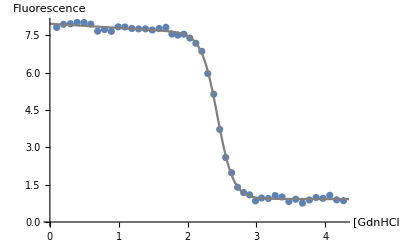

```mathematica
nlmchemdenat1errorfit=NonlinearModelFit[chemdenat1error,yobs,
{
{an,8},
{bn,-0.25},
{ad,1},
{bd,-0.02},
{dgh2o,0},
{m,0}
},
denat];
Show[chemdenat1errorp,Plot[nlmchemdenat1errorfit[x],{x,0,5},PlotStyle->Gray]]
```

```mathematica
(*b is the fraction native fit minus the y data*)
bchemdenat1error=fnchemdenat1[chemdenat1error[[All,1]]]-chemdenat1error[[All,2]];
(*a is the y data minus the fraction unfolded fit*)
achemdenat1error=chemdenat1error[[All,2]]-fuchemdenat1[chemdenat1error[[All,1]]];
(*get x1 y1 where x is [GdnHCl] and y is -RTln(b/a) (b/a = fu/fn = Keq)*)
dgvschemdenat1error=Transpose[{chemdenat1error[[All,1]],-R*T*Re[Log[bchemdenat1error/achemdenat1error]]}];
(*we know dGh2o is around -12*)
dgvschemdenat1errorp=ListPlot[dgvschemdenat1error,AxesLabel->{"[GdnHCl]","dG"},PlotRange->{{0,5},{-15,15}}];
```

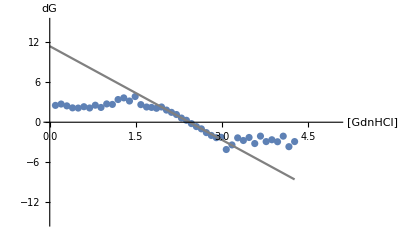

| Estimate | Standard Error | t-Statistic | P-Value
1 | 11.4314 | 0.279818 | 40.8528 | 1.65733×10^-7
x | -4.69774 | 0.126449 | -37.1514 | 2.66112×10^-7

dG is about 11.4314

```mathematica
(*get the best fit line of the dG vs [GdnHCl] plot where it is most linear (where it is unfolding and you're getting the actual b/a values)*)
dgvschemdenat1errorfit=LinearModelFit[dgvschemdenat1error[[20;;26]],x,x];
Show[dgvschemdenat1errorp,Plot[dgvschemdenat1errorfit[denat],{denat,0,Max[chemdenat1error[[All,1]]]},PlotStyle->Gray,PlotRange->{{0,5},{-15,15}}]]
dgvschemdenat1errorfit["ParameterTable"]
Print["dG is about ", dgvschemdenat1errorfit[0]]
```

```mathematica
Question 9
```

```mathematica
(*import and split apart the data*)
chemdenat2 = Transpose[Transpose[Import[ "/Users/Research/JHU_Class_Material/pchem/assignment_5/chemdenatdata2","Data"]][[3;;]]][[1]];
chemdenat2A=Transpose[{chemdenat2[[All,1]],chemdenat2[[All,2]]}][[1;;41]];
chemdenat2Ap=ListPlot[chemdenat2A,PlotRange->All,PlotStyle->Gray,PlotLegends->{"A"}];
chemdenat2B=Transpose[{chemdenat2[[All,1]],chemdenat2[[All,3]]}][[1;;41]];
chemdenat2Bp=ListPlot[chemdenat2B,PlotRange->All,PlotLegends->{"B"}];
```

```mathematica
(*get the best fit line for A using some guesses from the raw data graph and copying what Doug did in class*)
nlmchemdenat2A=NonlinearModelFit[chemdenat2A,yobs,
{
{an,3.6},
{bn,-0.25},
{ad,0.5},
{bd,-0.02},
{dgh2o,0},
{m,0}
},
denat];
nlmchemdenat2Ap=Plot[nlmchemdenat2A[denat],{denat,0,4},PlotRange->All,PlotStyle->Gray];
(*get the best fit line for B using some guesses from the raw data graph and copying what Doug did in class*)
nlmchemdenat2B=NonlinearModelFit[chemdenat2B,yobs,
{
{an,3.3},
{bn,-0.25},
{ad,0.5},
{bd,-0.02},
{dgh2o,0},
{m,0}
},
denat];
nlmchemdenat2Bp=Plot[nlmchemdenat2B[denat],{denat,0,4},PlotRange->All];
```

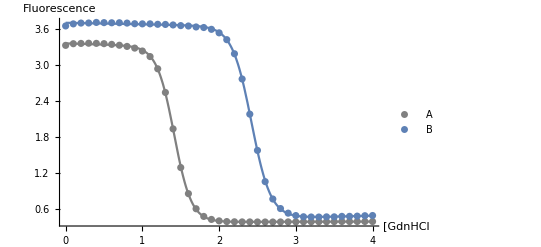

```mathematica
(*
(*overlay the raw data and the best fit lines*)
*)
Show[chemdenat2Ap,chemdenat2Bp,nlmchemdenat2Ap,nlmchemdenat2Bp,PlotRange->All,AxesLabel->{"[GdnHCl","Fluorescence"}]
```

```mathematica
(* for A
(*native baseline uses the first few points*)
*)
lnchemdenat2A=LinearModelFit[chemdenat2A[[3;;6]],x,x];
fnchemdenat2A[x_]:=lnchemdenat2A["BestFitParameters"][[1]]+(lnchemdenat2A["BestFitParameters"][[2]]*x);
(*unfolded baseline uses the last few points*)
luchemdenat2A=LinearModelFit[chemdenat2A[[-5;;]],x,x];
fuchemdenat2A[x_]:=luchemdenat2A["BestFitParameters"][[1]]+(luchemdenat2A["BestFitParameters"][[2]]*x);
(*The midpoint line is halfway between the equations that describe the fn and fu lines*)
lmchemdenat2A=Table[ {x,((lnchemdenat2A[x]-luchemdenat2A[x])/2)+luchemdenat2A[x]},{x,0,Max[chemdenat2A[[All,1]]]}];
Show[chemdenat2Ap,Plot[lnchemdenat2A[x],{x,0,Max[chemdenat2A[[All,1]]]}],Plot[luchemdenat2A[x],{x,0,Max[chemdenat2A[[All,1]]]}],
ListLinePlot[lmchemdenat2A,PlotStyle->Red]];
```

```mathematica
(* for B
(*native baseline uses the first few points*)
*)
lnchemdenat2B=LinearModelFit[chemdenat2B[[6;;8]],x,x];
fnchemdenat2B[x_]:=lnchemdenat2B["BestFitParameters"][[1]]+(lnchemdenat2B["BestFitParameters"][[2]]*x);
(*unfolded baseline uses the last few points*)
luchemdenat2B=LinearModelFit[chemdenat2B[[-4;;]],x,x];
fuchemdenat2B[x_]:=luchemdenat2B["BestFitParameters"][[1]]+(luchemdenat2B["BestFitParameters"][[2]]*x);
(*The midpoint line is halfway between the equations that describe the fn and fu lines*)
lmchemdenat2B=Table[ {x,((lnchemdenat2B[x]-luchemdenat2B[x])/2)+luchemdenat2B[x]},{x,0,Max[chemdenat2B[[All,1]]]}];
Show[chemdenat2Bp,Plot[lnchemdenat2B[x],{x,0,Max[chemdenat2B[[All,1]]]}],Plot[luchemdenat2B[x],{x,0,Max[chemdenat2B[[All,1]]]}],
ListLinePlot[lmchemdenat2B,PlotStyle->Red]];
```

```mathematica
(* for A
(*b is the fraction native fit minus the y data*)
*)
bchemdenat2A=fnchemdenat2A[chemdenat2A[[All,1]]]-chemdenat2A[[All,2]];
(*a is the y data minus the fraction unfolded fit*)
achemdenat2A=chemdenat2A[[All,2]]-fuchemdenat2A[chemdenat2A[[All,1]]];
(*get x1 y1 where x is [GdnHCl] and y is -RTln(b/a) (b/a = fu/fn = Keq)*)
dgvschemdenat2A=Transpose[{chemdenat2A[[All,1]],-R*T*Re[Log[bchemdenat2A/achemdenat2A]]}];
dgvschemdenat2Ap=ListPlot[dgvschemdenat2A,AxesLabel->{"[GdnHCl]","dG"},PlotRange->{{0,5},{-10,10}},PlotStyle->Gray,PlotLegends->{"A"}];
```

```mathematica
(* for B
(*b is the fraction native fit minus the y data*)
*)
bchemdenat2B=fnchemdenat2B[chemdenat2B[[All,1]]]-chemdenat2B[[All,2]];
(*a is the y data minus the fraction unfolded fit*)
achemdenat2B=chemdenat2B[[All,2]]-fuchemdenat2B[chemdenat2B[[All,1]]];
(*get x1 y1 where x is [GdnHCl] and y is -RTln(b/a) (b/a = fu/fn = Keq)*)
dgvschemdenat2B=Transpose[{chemdenat2B[[All,1]],-R*T*Re[Log[bchemdenat2B/achemdenat2B]]}];
dgvschemdenat2Bp=ListPlot[dgvschemdenat2B,AxesLabel->{"[GdnHCl]","dG"},PlotRange->{{0,5},{-10,10}},PlotLegends->{"B"}];
```

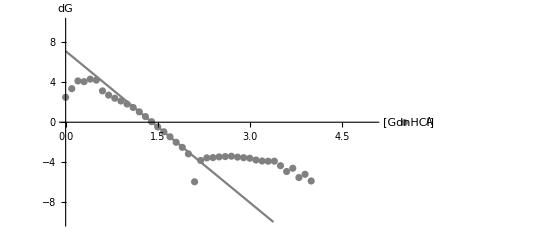

dG for A is about 7.12687

```mathematica
(* for A
(*get the best fit line of the dG vs [GdnHCl] plot where it is most linear (where it is unfolding and you're getting the actual b/a values)*)
*)
dgvschemdenat2Afit=LinearModelFit[dgvschemdenat2A[[13;;16]],x,x];
Show[dgvschemdenat2Ap,Plot[dgvschemdenat2Afit[denat],{denat,0,Max[chemdenat2A[[All,1]]]},PlotRange->{{0,5},{-10,10}},PlotStyle->Gray]]
Print["dG for A is about ", dgvschemdenat2Afit[0]]
```

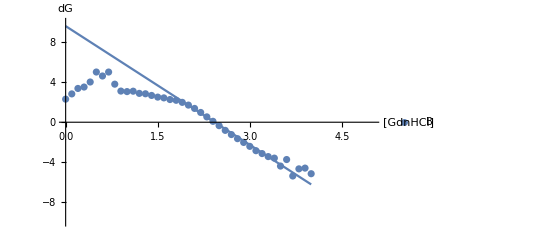

dG for B is about 9.63316

```mathematica
(* for B
(*get the best fit line of the dG vs [GdnHCl] plot where it is most linear (where it is unfolding and you're getting the actual b/a values)*)
*)
dgvschemdenat2Bfit=LinearModelFit[dgvschemdenat2B[[20;;26]],x,x];
Show[dgvschemdenat2Bp,Plot[dgvschemdenat2Bfit[denat],{denat,0,Max[chemdenat2B[[All,1]]]},PlotRange->Full]]
Print["dG for B is about ", dgvschemdenat2Bfit[0]]
```